#### 1)

```mathematica
f=1/x^3-1/(√x);
g=ArcTan[x]/Sin[x];
h=x^2 Exp[Cos[x]];
D[f,x]
D[g,x]
D[h,x]
```

-3/x^4+1/(2 x^(3/2))

Csc[x]/(1+x^2)-ArcTan[x] Cot[x] Csc[x]

2 ⅇ^Cos[x] x-ⅇ^Cos[x] x^2 Sin[x]

#### 2)

```mathematica
f=x^(1/3);
Series[f,{x,8,2}]//Normal
%/.{x->4.2}
Sqrt[4.2]
```

2+1/12 (-8+x)-1/288 (-8+x)^2

1.63319

2.04939

#### 3)

-6 x-3 x^2+8 x^3+6 x^4

-6-6 x+24 x^2+24 x^3

{{x→-1},{x→-1/2},{x→1/2}}

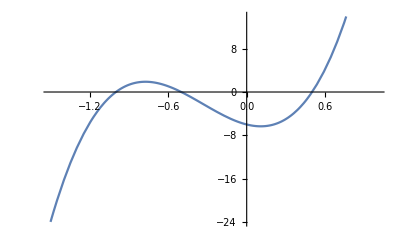

6 x^4+8 x^3-3 x^2-6 x

```mathematica
(x+1)(4 x^2-1)//Expand;
y1=Integrate[%,x]6//Expand
D[%,x]
Solve[%==0,x]
Plot[%%,{x,-1.5,1}]
y1//TeXForm
```

#### 4)

```mathematica
Apart[(3x-4)/(x^2-4x+4)]
Integrate[%,x]
```

2/(-2+x)^2+3/(-2+x)

-2/(-2+x)+3 Log[-2+x]

#### 5)

```mathematica
Integrate[√x-1/x^2,{x,1,4}]
Integrate[x/Sqrt[3 x^2+13],{x,1,2}]
```

47/12

1/3

#### 6)

{{x→-1},{x→1}}

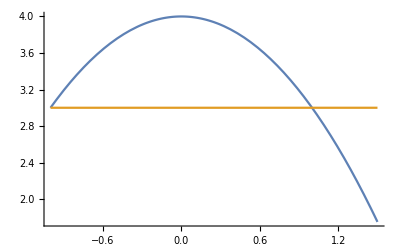

4/3

```mathematica
y1=4-x^2;
y2=3;
Solve[y1==y2,x]
Plot[{y1,y2},{x,-1,1.5}]
Integrate[y1-y2,{x,-1,1}]
```

#### 7)

-7+8 x

0

1

-6+x

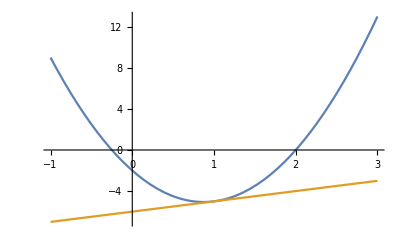

```mathematica
f1[x_]:=4 x^2-7x-2;
f1'[x]
x0=1;
f1[2]
f1'[x0]
g1[x_]:=f1'[x0](x-x0)+f1[x0];
g1[x]
Plot[{f1[x],g1[x]},{x,-1,3}]
```

#### 8)

```mathematica
y1=x;
y2=2x;
S=Integrate[(y2-y1),{x,0,4}]
Sy=Integrate[(y2-y1)x,{x,0,4}]
Sx=1/2Integrate[y2^2-y1^2,{x,0,4}]
```

8

64/3

32